## 1. naloga

```mathematica
?Graph
```

Graph[{e_1,e_2,…}] yields a graph with edges e_j.
Graph[{v_1,v_2,…},{e_1,e_2,…}] yields the graph with vertices v_i and edges e_j. 
Graph[{…,w_i[v_i,…],…},{…,w_j[e_j,…],…}] yields a graph with vertex and edge properties defined by the symbolic wrappers w_k.

Narišemo graf : 
(puščica: ecs de esc; ali pa jo označiš in pritisneš F1)

```mathematica
Graph[{a->b,a->d,b->a,b->d,c->a,c->e,d->c}]
```

-Graphics-

Naredimo matriko sosednosti:

```mathematica
AdjacencyMatrix[%]
```

SparseArray[<7>, {5, 5}]

Ker je v matriki veliko ničel, Mathematica varčuje s prostorom. Vendar nas zanima matrična oblika:

```mathematica
MatrixForm[%]
```

(0 | 1 | 1 | 0 | 0
1 | 0 | 1 | 0 | 0
0 | 0 | 0 | 1 | 0
1 | 0 | 0 | 0 | 1
0 | 0 | 0 | 0 | 0)

Narišemo graf preko matrike sosednosti :

```mathematica
AdjacencyGraph[%]
```

-Graphics-

Označimo vozlišča in povezave :

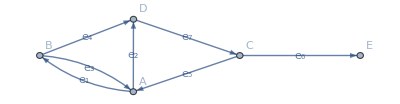

```mathematica
Graph[{a->b,a->d,b->a,b->d,c->a,c->e,d->c}, VertexLabels->{a->"A",b->"B",c->"C",d->"D",e->"E"},EdgeLabels->{a->b->"e_1",a->d->"e_2",b->a->"e_3",b->d->"e_4",c->a->"e_5",c->e->"e_6",d->c->"e_7"}]
```

```mathematica
Dodamo še uteži:
```

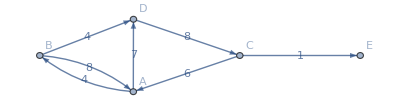

```mathematica
Graph[{a->b,a->d,b->a,b->d,c->a,c->e,d->c}, VertexLabels->{a->"A",b->"B",c->"C",d->"D",e->"E"},EdgeLabels->"EdgeWeight",EdgeWeight->{4,7,8,4,6,1,8}]
```

```mathematica
WeightedAdjacencyMatrix[%]
```

SparseArray[<7>, {5, 5}]

```mathematica
MatrixForm[%]
```

(0 | 4 | 7 | 0 | 0
8 | 0 | 4 | 0 | 0
0 | 0 | 0 | 8 | 0
6 | 0 | 0 | 0 | 1
0 | 0 | 0 | 0 | 0)

## 2. naloga

Razlika, če računamo maksimalni pretok z grafom ali z matriko!

Računamo z grafom: EdgeCapacity

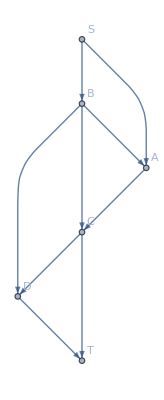

```mathematica
Graf =Graph[{s->a,s->b,b->a,a->c,b->c,b->d,c->d,c->t,d->t},VertexLabels->{a->"A",b->"B",c->"C",d->"D",s->"S",t->"T"},EdgeCapacity->{4,4,3,2,5,2,3,4,4}]
```

```mathematica
FindMaximumFlow[Graf,s,t]
```

6

Računamo z matriko: EdgeWeight

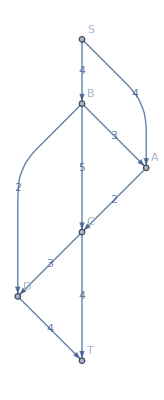

```mathematica
Graf2 =Graph[{s->a,s->b,b->a,a->c,b->c,b->d,c->d,c->t,d->t},VertexLabels->{a->"A",b->"B",c->"C",d->"D",s->"S",t->"T"},EdgeLabels->"EdgeWeight",EdgeWeight->{4,4,3,2,5,2,3,4,4}]
```

```mathematica
M=WeightedAdjacencyMatrix[Graf2]
```

SparseArray[<9>, {6, 6}]

```mathematica
MatrixForm[%]
```

(0 | 4 | 4 | 0 | 0 | 0
0 | 0 | 0 | 2 | 0 | 0
0 | 3 | 0 | 5 | 2 | 0
0 | 0 | 0 | 0 | 3 | 4
0 | 0 | 0 | 0 | 0 | 4
0 | 0 | 0 | 0 | 0 | 0)

```mathematica
FindMaximumFlow[M,1,6]
```

6